# Calculadora de Timer

## Para mbed LPC1768 @ 96MHz

Ernesto Palacios - mecatronica.mid@gmail.com

## Definicion de Constantes

```mathematica
SystemCoreClock = 96 10^6; (* Frecuencia Interna 96MHz *)
Tfeq = SystemCoreClock /4 ;(* Frecuencia del Timer *) 
ErrorTolerancia = 0.2 ;(* Error permisible en los registros *)
```

El valor de SystemCoreClock es el que viene por defecto para el Mbed LPC1768.
El valor de ErrorTolerancia, es el error permitido para los registros del Timer, si se excede este valor se imprimira una advertencia. Esto debido a que los valores de los registros son de tipo entero (uint32_t). no flotante.

IMPORTANTE:  Se asume que el Timer se resetea cada vez que el valor del registro MR  es alcanzado.

## Funciones de Calculo

### Funciones Básicas

#### Frecunencia de Bandera ( Match Register )

```mathematica
Fout[ PR_,MR_ ] := Module[ {exact,rounded,error},
exact = Tfeq/((PR+1) * (MR+1));

rounded =Round[exact];

error = N [exact-rounded];

{rounded,error}
]

Fout::usage=" Fout[ Prescaler, Match Register ]

Esta función permite conocer cual será la frecuncia con la que un Match Register [MR] se activará. Los parametros son PR = Prescaler, MR = valor del Match Register SALIDA EN HERTZ";
```

```mathematica
? Fout
```

Fout[ Prescaler, Match Register ]

Esta función permite conocer cual será la frecuncia con la que un Match Register [MR] se activará. Los parametros son PR = Prescaler, MR = valor del Match Register SALIDA EN HERTZ

#### Calcular Preescaler

```mathematica
PR[Fout_, MR_]:= Module[{exact,rounded,error},
exact = Tfeq/(Fout * (MR+1))-1;
rounded = Round[exact-1];

error = N[exact - rounded];

If[error > ErrorTolerancia , 
Print["Escoja un valor diferente para MR, el error es demasiado grande"]
];

If[rounded > 4294967295,
Print["Valor del Preescaler excedido, modifique las variables"]
];

{rounded, error}

]
PR::usage = " PR[ FreqSalida, MatchRegister ]
 Esta funcion calcula el Prescaler necesario para activar un Match Register [MR] a una frecuencia determinada [Tfeq]";
```

```mathematica
?PR
```

PR[ FreqSalida, MatchRegister ]
 Esta funcion calcula el Prescaler necesario para activar un Match Register [MR] a una frecuencia determinada [Tfeq]

#### Calcular Bandera ( Match Register )

```mathematica
MR[ Fout_,PR_ ]:=Module[{exact, rounded, error},
exact = Tfeq/((PR+1)*Fout)-1;
rounded = Round[exact];

error = N[exact - rounded];

If[error > ErrorTolerancia , 
Print["Escoja un valor diferente para PR, el error es demasiado grande"]
];

If[rounded > 4294967295,
Print["Valor de Match Register excedido, modifique las variables"]
];

{rounded, error}

]
MR::usage=" MR[ FreqSalida, Prescaler ]
Calcula el Match Register necesario para una salida Fout en hertz con un prescaler PR";
```

### Generador de Frecuencias

#### Pulse Train Output [ PTO ]

```mathematica
MR2[Freq_]:=Module[{ exact, error, register },

exact =  Tfeq/(Freq * 2)-1 ;

register = Round[exact];

error = exact - register;
{ register, error }

]
```

#### Match Register FQ

```mathematica
PTO[MR_]:=Module[{exact,error,Fq},

exact = Tfeq/(2*(MR+1));

Fq = Round[  exact];

error = N[exact-Fq];

{Fq,error}

]
```

```mathematica
200000-196721
```

3279

```mathematica
100000-99174
```

826

#### Tabla de Frecuencias

```mathematica
Table[{Fq,Part[PTO[Fq],1]},{Fq,119,200}]//MatrixForm
```

(119 | 100000
120 | 99174
121 | 98361
122 | 97561
123 | 96774
124 | 96000
125 | 95238
126 | 94488
127 | 93750
128 | 93023
129 | 92308
130 | 91603
131 | 90909
132 | 90226
133 | 89552
134 | 88889
135 | 88235
136 | 87591
137 | 86957
138 | 86331
139 | 85714
140 | 85106
141 | 84507
142 | 83916
143 | 83333
144 | 82759
145 | 82192
146 | 81633
147 | 81081
148 | 80537
149 | 80000
150 | 79470
151 | 78947
152 | 78431
153 | 77922
154 | 77419
155 | 76923
156 | 76433
157 | 75949
158 | 75472
159 | 75000
160 | 74534
161 | 74074
162 | 73620
163 | 73171
164 | 72727
165 | 72289
166 | 71856
167 | 71429
168 | 71006
169 | 70588
170 | 70175
171 | 69767
172 | 69364
173 | 68966
174 | 68571
175 | 68182
176 | 67797
177 | 67416
178 | 67039
179 | 66667
180 | 66298
181 | 65934
182 | 65574
183 | 65217
184 | 64865
185 | 64516
186 | 64171
187 | 63830
188 | 63492
189 | 63158
190 | 62827
191 | 62500
192 | 62176
193 | 61856
194 | 61538
195 | 61224
196 | 60914
197 | 60606
198 | 60302
199 | 60000
200 | 59701)

## Plots:

### Funciones sin aproximar para realizar las gráficas

```mathematica
Ft[ PR_,MR_ ] :=  Tfeq/(MR*2+1)
```

```mathematica
MRclean[ Fout_,PR_ ]:= Tfeq/(Fout*2)-1
```

#### Valor que debe adquirir MR para generar una frecuencia de 500 kHz (Frecuencia Máxima del Driver)

```mathematica
PTO[ 500000 ]
```

{23,0}

Con un preescaler de cero se debe setear MR con un valor de 23 para que la salida sea de 500 kHz

#### Valor que debe adquirir MR para una frecuencia de 10Hz (Frecuencia Mínima del Driver)

```mathematica
PTO[10]
```

{1199999,0}

Con un preescaler de cero se debe setear MR con un valor de 2.4M para generar una salida de 10Hz

#### Grafica de las frecuencias generadas a medida que varia MR

```mathematica
Plot[MRclean[x,0],{x,10,500000},
AxesLabel->{"Fout","Valor MR"}]
```

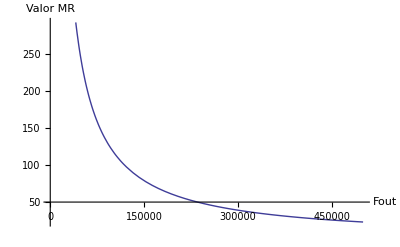

A bajos valores de MR se tiene grandes variaciones de las frecuencias, a medida que quiere frecuencias más bajas se tiene una mejor resolución

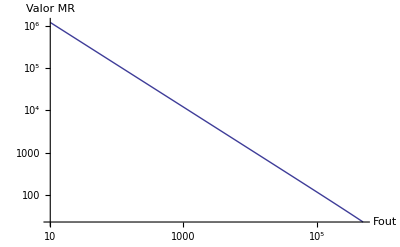

```mathematica
LogLogPlot[MRclean[x,0],{x,10,500000},
AxesLabel->{"Fout","Valor MR"}]
```

La misma función en una gráfica log-log

## Lista de Frecuencias Exactas.

La siguiente función imprimirá una lista de todas las frecuencias exactas que se pueden generar con el Timer2,  la columna de la izquierda es la frecuencia y la columna de la derecha es el valor que debe tener el MatchRegister

```mathematica
ErrorTolerancia = 0.6;(* Error permisible en los registros *)

For[ fq=80000,fq<100000,fq++ ,
If[ Part[PTO[fq],2]==0, 
Print[fq,"  ",Part[MR[fq,0],1]] ]
]

ErrorTolerancia = 0.2 ;(* Error permisible en los registros *)
```

93749  255

95999  249

99999  239